# Essentials of Programming in Mathematica

## Ch.1: Programming With Mathematica

## Exercises

1. Generate a random number between one and one hundred. Then create a vector of twelve random numbers between one and one hundred. Finally create a 4x4 array of such numbers and then compute the determinant of that array.

```mathematica
RandomReal[{1,100},{4,4}]//Det
```

1.81789×10^7

2. Using Table, create a 4x4 Hilbert matrix. The entry aij in row i, column j of the Hilbert matrix is given by . Check your solution against the built-in HilbertMatrix.

```mathematica
Table[1/(i+j-1),{i,1,4},{j,1,4}]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
HilbertMatrix[4]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
%5==%6
```

True

3. Add the two lists, {1, 2, 3, 4, 5} and {2, 4, 6, 8, 10}. Then multiply them element-wise. Finally, multiply the two lists as vectors (dot product).

```mathematica
{1,2,3,4,5}+{2,4,6,8,10}
{1,2,3,4,5}*{2,4,6,8,10}
{1,2,3,4,5}.{2,4,6,8,10}
```

{3,6,9,12,15}

{2,8,18,32,50}

110

4. Generate a list of the first 25 integers in five different ways.

```mathematica
Table[i,{i,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
Range[1,25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
doList={};
Do[AppendTo[doList,i],{i,1,25}];
doList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
forList={};
For[i=1,i≤ 25,i++,AppendTo[forList,i]];
forList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
whileList={};
i=1;
While[i≤ 25,AppendTo[whileList,i];i++];
whileList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

5. Add the integers one through one thousand in as many different ways as you can.

```mathematica
Sum[i,{i,1,1000}]
```

500500

```mathematica
ParallelSum[i,{i,1,1000}]
```

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

500500

```mathematica
Total[Range[1,1000]]
```

500500

```mathematica
Total[Table[i,{i,1,1000}]]
```

500500

```mathematica
i=0;
Do[i=i+j,{j,1,1000}];
i
```

500500

6. A 2×2 matrix can be created using lists such as {{a,b},{c,d}}. Deﬁne a 2×2 numerical matrix and then ﬁnd its inverse, determinant, transpose, and trace.

```mathematica
RandomReal[{0,1},{2,2}]//MatrixForm
```

(0.770901 | 0.772621
0.576254 | 0.497387)

```mathematica
Inverse[%18]//MatrixForm
```

(-8.04975 | 12.5042
9.32613 | -12.4763)

```mathematica
Det[%18]
```

-0.0617891

```mathematica
Transpose[%18]//MatrixForm
```

(0.770901 | 0.576254
0.772621 | 0.497387)

```mathematica
Tr[%18]
```

1.26829

## Ch.2: The Mathematica Language

## Examples

Random walk. Note that Accumulate is not the same as +=; it saves intermediate output.

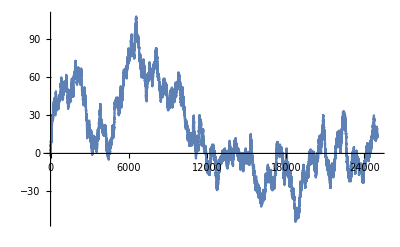

```mathematica
ListLinePlot[Accumulate[RandomChoice[{-1,0,1},{25000}]]]
```

Same but overlaying several random walks.

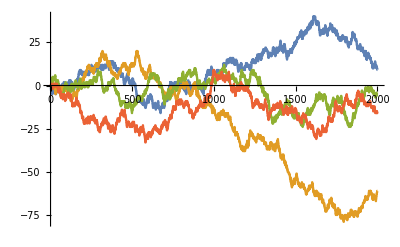

```mathematica
ListStepPlot[Table[Accumulate[RandomChoice[{-1,0,1},{2000}]],{4}]]
```

Random walk as a function

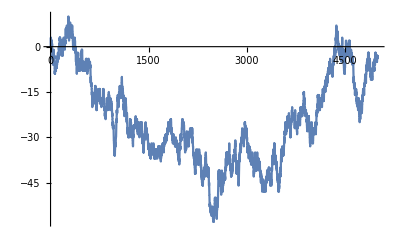

```mathematica
walk[t_]:=Module[{dirs,steps},
dirs={-1,0,1};
steps=RandomChoice[dirs,t];
Accumulate[steps]
];
walk[5000]//ListLinePlot
```

## Exercises

1. Determine if each of the following are atomic expressions. If the expression is not atomic, find its head.

```mathematica
AtomQ[8/5]
```

True

```mathematica
AtomQ[8/5+x]
Head[8/5+x]
```

False

Plus

```mathematica
AtomQ[{{a,b},{c,d}}]
Head[{{a,b},{c,d}}]
```

False

List

```mathematica
AtomQ["8/5+x"]
```

True

2. Give the full (internal) form of the expression a (b + c).

```mathematica
FullForm[a (b+c)]
```

Times[a,Plus[b,c]]

3. What is the traditional representation of Times [a, Power [Plus[b, c], –1]].

```mathematica
Times [a, Power [Plus[b, c], –1]]
```

a (b+c)^–

4. What is the part specification of the symbol b in the expression a x2 + b x + c?

```mathematica
Part[a x2+b x+c,2]
```

b x

5. What will be the result of evaluating each of the following? Use FullForm on the expressions to help you understand their structures.

```mathematica
FullForm[((x^2+y) z/w)[[2,1,2]]]
```

2

```mathematica
FullForm[(a/b)[[2,2]]]
```

-1

6. Use Level to find all the factors in the following expression. Then find all the terms inside the parentheses of the output.

```mathematica
LegendreP[5,x]
```

1/8 (15 x-70 x^3+63 x^5)

```mathematica
Level[%23[[2]],{2}]
```

{15,x,-70,x^3,63,x^5}

7. Explain why the following expression returns an integer instead of displaying the internal representation of the fraction.

8. Modify the code for the one-dimensional random walk in this section to create two-dimensional random walks.

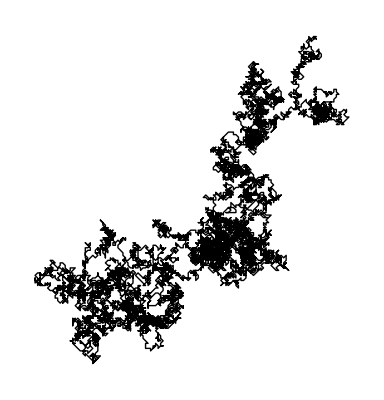

```mathematica
Graphics[Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]]
```

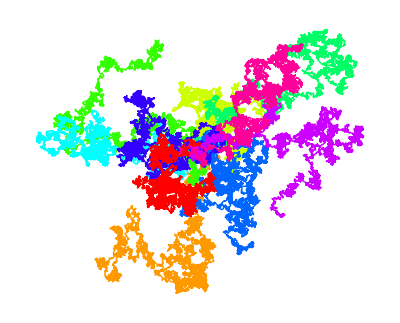

```mathematica
Graphics[Table[{Hue[i/10],Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]},{i,1,10}]
]
```

1. Is the expression 2 + π a number? Is it numeric? What is the difference?
It is not a number, it is a numeric.

```mathematica
NumberQ[2+π]
```

False

```mathematica
Head[2+π]
```

Plus

```mathematica
NumericQ[2+π]
```

True

2. Convert the base 10 integer 65 to base 2. Then convert back to base 10.

```mathematica
BaseForm[65,2]
```

```mathematica
Subscript["1000001", "2"]
```

65

```mathematica
2^^1000001
```

65

3. Define a function complexToPolar that converts complex numbers to their polar representations. Then, convert the numbers 3 + 3 i and π/3 to polar form.

```mathematica
complexToPolar[num_]:=Module[{θ,r},
r=Abs[num];
θ=Arg[num];
{r,θ}
];
```

```mathematica
complexToPolar[3+3ⅈ]
```

{3 √2,π/4}

```mathematica
AbsArg[3+3ⅈ]
```

{3 √2,π/4}

4. Use NumberForm to display an approximate number with exactly four precise digits and three digits to the right of the decimal. Then use PaddedForm to display the numbers in the following vector with precisely two digits to the right of the decimal.

```mathematica
NumberForm[N[Pi],{4,3}]
```

3.142

```mathematica
vec=RandomReal[{0,1},8]
```

{0.814211,0.551942,0.960738,0.439451,0.0299773,0.148097,0.153071,0.702443}

```mathematica
PaddedForm[vec,{3,2}]
```

{ 0.81, 0.55, 0.96, 0.44, 0.03, 0.15, 0.15, 0.70}

5. Make a histogram of the frequencies of the first 100 000 digits of π. It is an open problem in number theory as to whether the digits are normal, meaning that each of the digits zero through nine occur with about the same frequency in the decimal expansion of π. See Bailey (2012) for more information on normality and the digits of π.

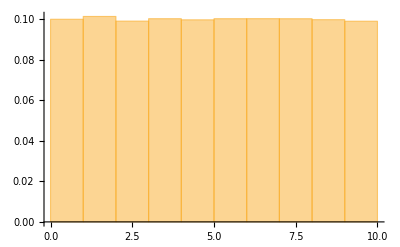

```mathematica
Histogram[RealDigits[N[Pi,100000]],Automatic,"Probability"]
```

6. Convert each of the characters in a string such as “Apple” to their eight-bit binary character code representation.

```mathematica
ToCharacterCode/@Characters["Apple"]//Flatten
```

{65,112,112,108,101}

```mathematica
IntegerDigits[%,2,8]
```

{{0,1,0,0,0,0,0,1},{0,1,1,1,0,0,0,0},{0,1,1,1,0,0,0,0},{0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,1}}

7. Extract the first 5000 digits in the decimal expansion of 1/17 or any other rational number. Then play them using ListPlay which emits sound whose amplitude is given by the sequence of digits. Compare with the first 5000 digits of π.

```mathematica
N[1/17,10]
```

0.05882352941

8. Graphs consist of a set of vertices and edges connecting some subset of those vertices. They are implemented in Mathematica with Graph, which takes two arguments: a list of vertices and a list of edges. Create a random graph on n vertices by choosing m edges from the  possible edges. Such random graphs are commonly specified as G(n, m) and are essentially the model upon which the built-in RandomGraph is based.

```mathematica
makeEdges[n_,m_]:=Subsets[Range[1,n],{2}]//RandomSample[#,m]&//EdgeList;
```

```mathematica
makeEdges[20,5]
```

{2<->16,11<->20,10<->12,6<->9,9<->19}

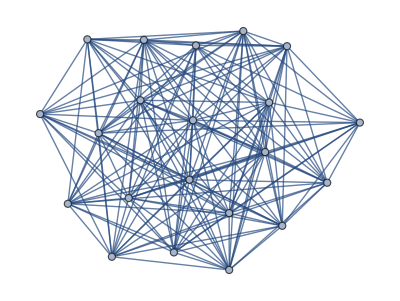

```mathematica
Graph[makeEdges[21,167]]
```

9. RandomReal by default outputs numbers uniformly distributed on the interval [0, 1]. Bias the random number generator towards the lower end of this interval giving a histogram similar to those below.

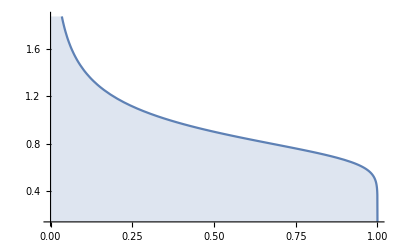

```mathematica
Plot[PDF[BetaDistribution[.75,1.1],x],{x,0,1},Filling->Axis]
```

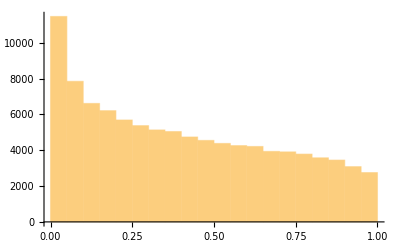

```mathematica
RandomVariate[BetaDistribution[.75,1.1],100000]//Histogram
```

10. Information theory, as conceived by Claude Shannon in the 1940s and 1950s, was originally interested in maximizing the amount of data that can be stored and retrieved over some channel such as a telephone line. Shannon devised a measure, now called the entropy, that gives the theoretical maxima for such a signal. Entropy can be thought of as the average uncertainty of a single random variable and is computed by the following, where p(x) is the probability of event x over a domain X:
H(X) = –∑x∈X p(x) log2 p(x)
Generate a plot of the entropy (built into Mathematica as Entropy) as a function of success probability.

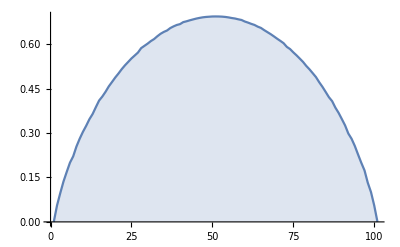

```mathematica
Entropy/@Table[RandomVariate[BernoulliDistribution[p],100000],{p,0,1,0.01}]//ListLinePlot[#,Filling->Axis]&
```

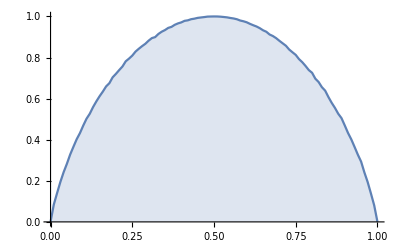

```mathematica
Table[{p,Entropy[2,RandomVariate[BernoulliDistribution[p],100000]]},{p,0,1,0.01}]//ListLinePlot[#,Filling->Axis]&
```

1. Create a function reciprocal[] that returns the reciprocal of the fraction a/b. Check your answer with numeric and symbolic fractions as well as with fractions containing zero in the numerator.

```mathematica
reciprocal[Rational[a_,b_]]:=Rational[b,a];
```

```mathematica
reciprocal[5/2]
```

2/5

2. Using Total, create a function to sum the first n positive integers.

```mathematica
sumInt[n_]:=Total[Range[1,n]];
```

```mathematica
sumInt[5]
```

15

3. Create a function to compute the sum of the digits of any integer. Write an additional rule to give the sum of the base-b digits of an integer. Then use your function to compute the Hamming weight of any integer: the Hamming weight of an integer is given by the number of ones in the binary representation of that number. It has wide use in computer science (modular exponentiation and hash tables), cryptography, and coding theory (Knuth 2011).

```mathematica
hammingWeight[int_]:=Module[{sumDig,sumB,hamW},
sumDig=IntegerDigits[int]//Total;
sumB=IntegerDigits[int,2]//Total;
hamW=IntegerDigits[int,2]//Count[#,1]&;
{sumDig,sumB,hamW}
];
hammingWeight[24355]
```

{19,9,9}

4. Write a function sumsOfCubes [n] that takes a positive integer argument n and computes the sums of cubes of the digits of n (Hayes 1992).

```mathematica
sumsOfCubes[n_]:=Total[IntegerDigits[n]^3];
```

```mathematica
sumsOfCubes[124]
```

73

8. Create a piecewise-defined function g(x) based on the following; plot the function from –2 to 0.

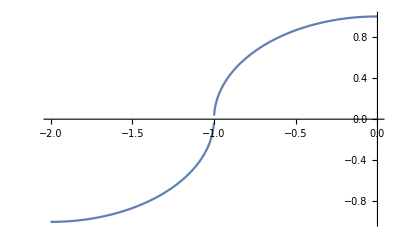

```mathematica
g[x_]:=Piecewise[{
{-Sqrt[1-(x+2)^2],-2≤x≤-1},
{Sqrt[1-x^2],x<0}
}];
Plot[g[x],{x,-2,0}]
```

9. The built-in function RotateRight rotates the elements in a list one place to the right with the last element swinging around to the front. Create a function IntegerRotateRight [n] that takes an integer n and returns an integer with the original digits rotated one place to the right.

```mathematica
RotateRight[{a,b,c,d,e}]
```

{e,a,b,c,d}

```mathematica
IntegerRotateRight[n_]:=Prepend[IntegerDigits[n]//Most,IntegerDigits[n]//Last]//Flatten;
```

```mathematica
IntegerRotateRight[142857]
```

714285

```mathematica
Divisors[%]//Position[#,142857]&
```

{{62}}

10. The Champernowne constant is a famous number that is created by concatenating successive integers and interpreting them as decimal digits. Concatenation can used to create integers also. Create a function to generate the nth Smarandache-Wellin number, formed by concatenating the digits of successive primes. The first such number is 2, then 23, then 235, followed by 2357, 235711, and so on. Numerous open questions exist about these numbers: for example it is not known if an infinite number of them are prime; see Crandall and Pomerance (2005) and Sloane (A019518).

```mathematica
N[ChampernowneNumber[10],31]
```

0.123456789101112131415161718192

```mathematica
smNumber[n_]:=Table[Prime[i],{i,1,n}]//IntegerDigits//Flatten//FromDigits;
smNumber[5]
```

235711

```mathematica
Table[smNumber[i],{i,1,10}]
```

{2,23,235,2357,235711,23571113,2357111317,235711131719,23571113171923,2357111317192329}